# Project report

## Pressure controller installation

D Malan

Department of Chemistry
University of Pretoria

3 February 2020

## Introduction

When the column broke near the detector inlet (as previously reported), carbon dioxide at high pressure entered the GC system. It blew through the detector and entered the inlet. The high pressure damaged the gauge, rendering it useless

## Experimental

The damaged gauge was removed and inspected it to see if it might be repaired.

A used pressure controller and gauge combination was found. A suitable set of connectors was found and the unit was connected and tested.

The controller and gauge was mounted on top of the GC with a single screw. The unit contains a shut-off valve: to prevent this valve from being inadvertently closed, it was splinted open with a heat-shrink tubing and a short length of stiff rod.

The flow through the column was measured by connecting a comparable length of column to the inlet and measuring the flow at different pressure settings, using a bubble flow meter and a hand-held stopwatch.

## Calculations

```mathematica
ppsi = Quantity[1, "PoundsForce"]/Quantity[1, "Inches"]^2
```

1 lbf/in^2

```mathematica
pkgcm = Quantity[1, "KilogramsForce"]/Quantity[1, "Centimeters"]^2
```

1 kgf/cm^2

```mathematica
pvap = Quantity[5000.0, "Kilopascals"]
```

5000. kPa

```mathematica
UnitConvert[1.0*ppsi, QuantityUnit[pkgcm]]
```

0.070307 kgf/cm^2

```mathematica
UnitConvert[1.4*pkgcm, QuantityUnit[ppsi]]
```

19.9127 lbf/in^2

```mathematica
UnitConvert[pvap, QuantityUnit[ppsi]]
```

725.189 lbf/in^2

```mathematica
flowfile ="C:\\Users\\fskdm\\My PhD\\Projects\\2020_02_03_Gauge_Install\\2020_02_03_Column_Flow.xlsx"
```

C:\Users\fskdm\My PhD\Projects\2020_02_03_Gauge_Install\2020_02_03_Column_Flow.xlsx

```mathematica
data =Import[flowfile];
```

```mathematica
TableForm[data[[1]]]
```

Mon 3 Feb 2020 15:30:00GMT+2. | Column flow |  |  |  | 
 | Room temperature: 22°C |  |  |  | 
 | Pressure: | 1.4 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 8. | 7.5 | 0.125 | 64. | 
 | 10. | 9.7 | 0.161667 | 61.8557 | 
 | 10. | 9.74 | 0.162333 | 61.6016 | 
 |  |  |  | 62.4858 | Average
 |  |  |  |  | 
 | Pressure: | 1.2 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 10. | 11.6 | 0.193333 | 51.7241 | 
 | 10. | 12.02 | 0.200333 | 49.9168 | 
 | 10. | 11.55 | 0.1925 | 51.9481 | 
 |  |  |  | 51.1963 | Average
 |  |  |  |  | 
 | Pressure: | 1. | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 10. | 15.06 | 0.251 | 39.8406 | 
 | 10. | 15.17 | 0.252833 | 39.5517 | 
 | 10. | 15.19 | 0.253167 | 39.4997 | 
 |  |  |  | 39.6307 | 
 |  |  |  |  | 
 | Pressure: | 0.8 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 10. | 20.58 | 0.343 | 29.1545 | 
 | 2. | 4.09 | 0.0681667 | 29.3399 | 
 | 8. | 16.24 | 0.270667 | 29.5567 | 
 |  |  |  | 29.3503 | 
 |  |  |  |  | 
 | Pressure: | 0.6 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 2. | 5.79 | 0.0965 | 20.7254 | 
 | 2. | 5.79 | 0.0965 | 20.7254 | 
 | 2. | 5.7 | 0.095 | 21.0526 | 
 |  |  |  | 20.8345 | 
 |  |  |  |  | 
 | Pressure: | 0.4 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 2. | 9.65 | 0.160833 | 12.4352 | 
 | 2. | 9.66 | 0.161 | 12.4224 | 
 | 2. | 9.64 | 0.160667 | 12.4481 | 
 |  |  |  | 12.4352 |

```mathematica
averagelines = 1+Range[6]*8
```

{9,17,25,33,41,49}

```mathematica
flows = data[[1,averagelines,5]]
```

{62.4858,51.1963,39.6307,29.3503,20.8345,12.4352}

```mathematica
pressurelines = 3+(Range[6]-1)*8
```

{3,11,19,27,35,43}

```mathematica
pressures =data[[1, pressurelines,3]]/0.070307
```

{19.9127,17.068,14.2233,11.3787,8.534,5.68933}

```mathematica
plotdata = Partition[Riffle[pressures, flows],2]
```

{{19.9127,62.4858},{17.068,51.1963},{14.2233,39.6307},{11.3787,29.3503},{8.534,20.8345},{5.68933,12.4352}}

```mathematica
fit = Fit[plotdata, {1,x},x]
```

-9.2193+3.53161 x

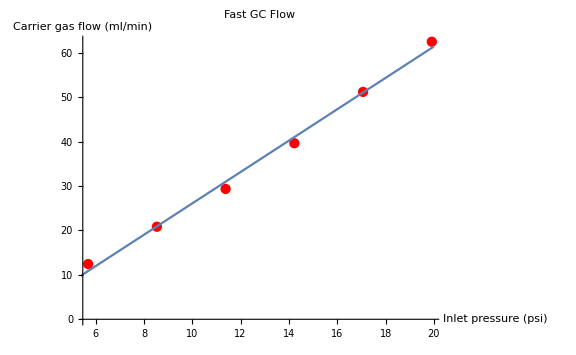

```mathematica
Show[
ListPlot[plotdata
, PlotLabel->"Fast GC Flow"
, AxesLabel->{"Inlet pressure\n(psi)","Carrier gas flow\n(ml/min)"}
, PlotStyle->Red
, ImageSize->Large
]
,Plot[fit,{x,5,20}]
]
```

## Results

### Inspection

The needle of the gauge has wound around and is pressing against the low-end stop from the wrong side. There are visible bulges on the inner side of the Bourdon tube.

```mathematica
-Graphics--Graphics-
```

### New installation

This is what the new installation looks like. The controller can smoothly control the pressure. Note that the pneumatics of the Varian 3300 GC is not being used at all to control the carrier gas: the pressure indicated on the Varian gauge is the supply pressure.

### Flow

The pressure of the carrier gas can be controlled up to 19 psi (1.4 kg/cm^2). The flow is close enough to a linear function of the inlet pressure.

## Discussion

I would have preferred to just install a new gauge for the previous controller, but a few issues meant that installing the new controller was the faster option. I have a drawer full of gas pressure gauges, but they would have to fit in the space available, and have suitable connections. They all have different units of measure, which could lead to confusion. They have different measurement ranges.

The chosen gauge is calibrated in the horrible unit of km/cm^2, and has a range of 0 to 2, which corresponds to 0 to 30 psi. Because the fast GC column is short, the required column head pressure for suitable flow is low, and I normally use a pressure of 10 psi (0.7 kg/cm^2). This controller and gauge combination might be more suitable than the previous one, which had problems controlling below 10 psi.

The damage to the gauges indicates the magnitude of the pressure difference between the ends of the coaxial heater. The vapour pressure of the carbon dioxide in the cylinder is 5000 kPa, or 725 psi. This means that the gauge experienced a pressure in excess of ten times the indicated range. On previous occasions when the column had broken inside the coaxial heater it had happened near the inlet end, and there was no obvious sign that it had happened, except that the FID flame was blown out. It was diagnosed by detecting the leak at the cryogen outlet.

## Conclusion

A new pressure controller and pressure gauge have been installed for the fast GC. They can regulate pressure up to 19 psi, which would be adequate for the fast GC application.

## Recommendations

Install an overpressure vent in the inlet to prevent future damage.

Switch to a solid-state electronic pressure gauge.

Switch to electronic flow control.